```mathematica
(*solving with initial condition x(0)=a*)
```

```mathematica
DSolve[{x'[t]==x[t](1-x[t]),x[0]==a},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(a ⅇ^t)/(1-a+a ⅇ^t)}}

```mathematica
DSolve[{x'[t]==-x[t](1-x[t]),x[0]==a},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→-a/(-a-ⅇ^t+a ⅇ^t)}}

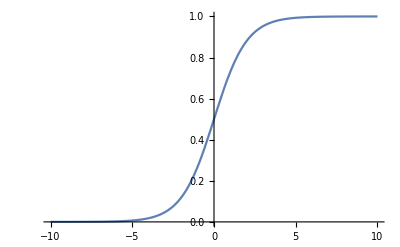

```mathematica
Plot[1/(1+E^-t),{t,-10,10}]
```